```mathematica
ClearAll["Global`*"]
```

### Pion

```mathematica
idealπ=
{{7.17752430*10^-03,2.18980123*10^+02},{3.78993630*10^-02,2.18639053*10^+02},{9.35073360*10^-02,2.13122813*10^+02},{1.74611500*10^-01,1.87502522*10^+02},{2.82124830*10^-01,1.40816711*10^+02},{4.17333600*10^-01,9.17229312*10^+01},{5.81993540*10^-01,5.33718276*10^+01},{7.78479140*10^-01,2.81854113*10^+01},{1.01002170*10^+00,1.35314490*10^+01},{1.28110830*10^+00,5.85498876*10^+00},{1.59819070*10^+00,2.24466924*10^+00},{1.97106870*10^+00,7.41926889*10^-01},{2.41596300*10^+00,2.02085807*10^-01},{2.96389860*10^+00,4.16237710*10^-02}(*,{3.69431420*10^+00,5.20294673*10^-03}*)};


shear14π={{7.17752430*10^-03,2.18941609*10^+02},{3.78993630*10^-02,2.18475028*10^+02},{9.35073360*10^-02,2.12482537*10^+02},{1.74611500*10^-01,1.86294262*10^+02},{2.82124830*10^-01,1.39469211*10^+02},{4.17333600*10^-01,9.06810759*10^+01},{5.81993540*10^-01,5.27974970*10^+01},{7.78479140*10^-01,2.80047913*10^+01},{1.01002170*10^+00,1.35767643*10^+01},{1.28110830*10^+00,5.97430037*10^+00},{1.59819070*10^+00,2.34985823*10^+00},{1.97106870*10^+00,8.05424170*10^-01},{2.41596300*10^+00,2.30489415*10^-01},{2.96389860*10^+00,5.07293523*10^-02}(*,{3.69431420*10^+00,6.95914088*10^-03}*)};

shearCEπ=
{{7.17752430*10^-03,2.19809107*10^+02},{3.78993630*10^-02,2.18628923*10^+02},{9.35073360*10^-02,2.10295605*10^+02},{1.74611500*10^-01,1.82504816*10^+02},{2.82124830*10^-01,1.36547711*10^+02},{4.17333600*10^-01,8.93767572*10^+01},{5.81993540*10^-01,5.26018957*10^+01},{7.78479140*10^-01,2.82617661*10^+01},{1.01002170*10^+00,1.38791827*10^+01},{1.28110830*10^+00,6.17246886*10^+00},{1.59819070*10^+00,2.44181264*10^+00},{1.97106870*10^+00,8.35470607*10^-01},{2.41596300*10^+00,2.36207536*10^-01},{2.96389860*10^+00,5.06498596*10^-02}(*,{3.69431420*10^+00,6.62814423*10^-03}*)};

shearmodπ ={{7.17752430*10^-03,2.19468203*10^+02},{3.78993630*10^-02,2.18479602*10^+02},{9.35073360*10^-02,2.10708864*10^+02},{1.74611500*10^-01,1.83101281*10^+02},{2.82124830*10^-01,1.36729494*10^+02},{4.17333600*10^-01,8.91567036*10^+01},{5.81993540*10^-01,5.22365786*10^+01},{7.78479140*10^-01,2.79425458*10^+01},{1.01002170*10^+00,1.36736840*10^+01},{1.28110830*10^+00,6.06813954*10^+00},{1.59819070*10^+00,2.40014995*10^+00},{1.97106870*10^+00,8.23227763*10^-01},{2.41596300*10^+00,2.34151348*10^-01},{2.96389860*10^+00,5.07809141*10^-02}(*,{3.69431420*10^+00,6.78443278*10^-03}*)};

bulk14π = {{7.17752430*10^-03,2.20147953*10^+02},{3.78993630*10^-02,2.19822473*10^+02},{9.35073360*10^-02,2.14202215*10^+02},{1.74611500*10^-01,1.87742221*10^+02},{2.82124830*10^-01,1.39541814*10^+02},{4.17333600*10^-01,8.92614915*10^+01},{5.81993540*10^-01,5.05857293*10^+01},{7.78479140*10^-01,2.57543886*10^+01},{1.01002170*10^+00,1.17465146*10^+01},{1.28110830*10^+00,4.71863679*10^+00},{1.59819070*10^+00,1.61602906*10^+00},{1.97106870*10^+00,4.44584684*10^-01},{2.41596300*10^+00,8.61257756*10^-02},{2.96389860*10^+00,7.00189543*10^-03}(*,{3.69431420*10^+00,-1.32561622*10^-03}*)};

bulkCEπ=
{{7.17752430*10^-03,2.17645932*10^+02},{3.78993630*10^-02,2.17388125*10^+02},{9.35073360*10^-02,2.11536505*10^+02},{1.74611500*10^-01,1.83248323*10^+02},{2.82124830*10^-01,1.33182328*10^+02},{4.17333600*10^-01,8.31643289*10^+01},{5.81993540*10^-01,4.61525446*10^+01},{7.78479140*10^-01,2.31061309*10^+01},{1.01002170*10^+00,1.04190871*10^+01},{1.28110830*10^+00,4.17525948*10^+00},{1.59819070*10^+00,1.45177493*10^+00},{1.97106870*10^+00,4.21483034*10^-01},{2.41596300*10^+00,9.55774645*10^-02},{2.96389860*10^+00,1.47290034*10^-02}(*,{3.69431420*10^+00,9.99032416*10^-04}*)};

bulkmodπ=
{{7.17752430*10^-03,2.17462697*10^+02},{3.78993630*10^-02,2.17184880*10^+02},{9.35073360*10^-02,2.11246389*10^+02},{1.74611500*10^-01,1.82678572*10^+02},{2.82124830*10^-01,1.32433831*10^+02},{4.17333600*10^-01,8.26033212*10^+01},{5.81993540*10^-01,4.58765858*10^+01},{7.78479140*10^-01,2.30338767*10^+01},{1.01002170*10^+00,1.04490449*10^+01},{1.28110830*10^+00,4.23571087*10^+00},{1.59819070*10^+00,1.50463889*10^+00},{1.97106870*10^+00,4.54427804*10^-01},{2.41596300*10^+00,1.11055403*10^-01},{2.96389860*10^+00,1.99930358*10^-02}(*,{3.69431420*10^+00,2.08565786*10^-03}*)};


shearbulk14π={{7.17752430*10^-03,2.19997608*10^+02},{3.78993630*10^-02,2.19554671*10^+02},{9.35073360*10^-02,2.13496334*10^+02},{1.74611500*10^-01,1.86529187*10^+02},{2.82124830*10^-01,1.38236808*10^+02},{4.17333600*10^-01,8.82877077*10^+01},{5.81993540*10^-01,5.00809380*10^+01},{7.78479140*10^-01,2.56203553*10^+01},{1.01002170*10^+00,1.18069388*10^+01},{1.28110830*10^+00,4.83088577*10^+00},{1.59819070*10^+00,1.70678053*10^+00},{1.97106870*10^+00,4.96179941*10^-01},{2.41596300*10^+00,1.08010319*10^-01},{2.96389860*10^+00,1.36498350*10^-02}(*,{3.69431420*10^+00,-1.20713861*10^-04}*)};

(*shearbulk14test = Table[{idealπ[[i,1]], shear14π[[i,2]]+bulk14π[[i,2]]-idealπ[[i,2]]},{i,1,Length[idealπ]}]*)

shearbulkCEπ={{7.17752430*10^-03,2.17800547*10^+02},{3.78993630*10^-02,2.16763659*10^+02},{9.35073360*10^-02,2.08377358*10^+02},{1.74611500*10^-01,1.78328623*10^+02},{2.82124830*10^-01,1.29184420*10^+02},{4.17333600*10^-01,8.10749623*10^+01},{5.81993540*10^-01,4.55402373*10^+01},{7.78479140*10^-01,2.32332710*10^+01},{1.01002170*10^+00,1.07486832*10^+01},{1.28110830*10^+00,4.45181815*10^+00},{1.59819070*10^+00,1.61412214*10^+00},{1.97106870*10^+00,4.94842338*10^-01},{2.41596300*10^+00,1.21091962*10^-01},{2.96389860*10^+00,2.11452436*10^-02},{3.69431420*10^+00,1.95353662*10^-03}};

shearbulkmodπ={{7.17752430*10^-03,2.17461658*10^+02},{3.78993630*10^-02,2.16502751*10^+02},{9.35073360*10^-02,2.08372082*10^+02},{1.74611500*10^-01,1.78486968*10^+02},{2.82124830*10^-01,1.29338751*10^+02},{4.17333600*10^-01,8.12620992*10^+01},{5.81993540*10^-01,4.57354686*10^+01},{7.78479140*10^-01,2.33988785*10^+01},{1.01002170*10^+00,1.08708982*10^+01},{1.28110830*10^+00,4.53430589*10^+00},{1.59819070*10^+00,1.66435877*10^+00},{1.97106870*10^+00,5.21484477*10^-01},{2.41596300*10^+00,1.32782734*10^-01},{2.96389860*10^+00,2.50570238*10^-02},{3.69431420*10^+00,2.77343292*10^-03}};
```

### Kaon

```mathematica
idealK={{7.17752430*10^-03,2.06110890*10^+01},{3.78993630*10^-02,2.06048162*10^+01},{9.35073360*10^-02,2.05602452*10^+01},{1.74611500*10^-01,2.03317196*10^+01},{2.82124830*10^-01,1.94755231*10^+01},{4.17333600*10^-01,1.73329268*10^+01},{5.81993540*10^-01,1.37375683*10^+01},{7.78479140*10^-01,9.46455955*10^+00},{1.01002170*10^+00,5.62641051*10^+00},{1.28110830*10^+00,2.87935752*10^+00},{1.59819070*10^+00,1.25993536*10^+00},{1.97106870*10^+00,4.63063911*10^-01},{2.41596300*10^+00,1.37670393*10^-01},{2.96389860*10^+00,3.05688769*10^-02}(*,{3.69431420*10^+00,4.09521636*10^-03}*)};

shear14K = {{7.17752430*10^-03,2.07289682*10^+01},{3.78993630*10^-02,2.07146212*10^+01},{9.35073360*10^-02,2.06298604*10^+01},{1.74611500*10^-01,2.03026885*10^+01},{2.82124830*10^-01,1.93067572*10^+01},{4.17333600*10^-01,1.70669117*10^+01},{5.81993540*10^-01,1.34872164*10^+01},{7.78479140*10^-01,9.31642933*10^+00},{1.01002170*10^+00,5.58630386*10^+00},{1.28110830*10^+00,2.90144442*10^+00},{1.59819070*10^+00,1.29691378*10^+00},{1.97106870*10^+00,4.90339132*10^-01},{2.41596300*10^+00,1.51141371*10^-01},{2.96389860*10^+00,3.51202699*10^-02}(*,{3.69431420*10^+00,4.99261015*10^-03}*)};

shearCEK={{7.17752430*10^-03,2.08903882*10^+01},{3.78993630*10^-02,2.08664777*10^+01},{9.35073360*10^-02,2.07345108*10^+01},{1.74611500*10^-01,2.02948400*10^+01},{2.82124830*10^-01,1.91526890*10^+01},{4.17333600*10^-01,1.68394385*10^+01},{5.81993540*10^-01,1.33180111*10^+01},{7.78479140*10^-01,9.26377133*10^+00},{1.01002170*10^+00,5.61053826*10^+00},{1.28110830*10^+00,2.94133135*10^+00},{1.59819070*10^+00,1.32209587*10^+00},{1.97106870*10^+00,4.99596191*10^-01},{2.41596300*10^+00,1.52680625*10^-01},{2.96389860*10^+00,3.48219404*10^-02}(*,{3.69431420*10^+00,4.79076575*10^-03}*)};

shearmodK={{7.17752430*10^-03,2.08766954*10^+01},{3.78993630*10^-02,2.08569771*10^+01},{9.35073360*10^-02,2.07451309*10^+01},{1.74611500*10^-01,2.03499194*10^+01},{2.82124830*10^-01,1.92533014*10^+01},{4.17333600*10^-01,1.69378962*10^+01},{5.81993540*10^-01,1.33632199*10^+01},{7.78479140*10^-01,9.25752829*10^+00},{1.01002170*10^+00,5.58771924*10^+00},{1.28110830*10^+00,2.92591777*10^+00},{1.59819070*10^+00,1.31745144*10^+00},{1.97106870*10^+00,5.00327369*10^-01},{2.41596300*10^+00,1.54242123*10^-01},{2.96389860*10^+00,3.56604911*10^-02},{3.69431420*10^+00,5.01408033*10^-03}};

bulk14K = {{7.17752430*10^-03,2.06413919*10^+01},{3.78993630*10^-02,2.06358089*10^+01},{9.35073360*10^-02,2.05939397*10^+01},{1.74611500*10^-01,2.03656687*10^+01},{2.82124830*10^-01,1.94828016*10^+01},{4.17333600*10^-01,1.72497925*10^+01},{5.81993540*10^-01,1.35044862*10^+01},{7.78479140*10^-01,9.09231259*10^+00},{1.01002170*10^+00,5.20190326*10^+00},{1.28110830*10^+00,2.50517205*10^+00},{1.59819070*10^+00,9.95938026*10^-01},{1.97106870*10^+00,3.12858742*10^-01},{2.41596300*10^+00,7.00661984*10^-02},{2.96389860*10^+00,7.93747800*10^-03}(*,{3.69431420*10^+00,-6.04633361*10^-04}*)};

bulkCEK={{7.17752430*10^-03,2.11343992*10^+01},{3.78993630*10^-02,2.11296514*10^+01},{9.35073360*10^-02,2.10918286*10^+01},{1.74611500*10^-01,2.08716628*10^+01},{2.82124830*10^-01,1.99852640*10^+01},{4.17333600*10^-01,1.76869720*10^+01},{5.81993540*10^-01,1.37809824*10^+01},{7.78479140*10^-01,9.18212270*10^+00},{1.01002170*10^+00,5.18202396*10^+00},{1.28110830*10^+00,2.46839396*10^+00},{1.59819070*10^+00,9.82720130*10^-01},{1.97106870*10^+00,3.18855213*10^-01},{2.41596300*10^+00,7.98926882*10^-02},{2.96389860*10^+00,1.37127714*10^-02}(*,{3.69431420*10^+00,1.12764724*10^-03}*)};

bulkmodK={{7.17752430*10^-03,2.12767159*10^+01},{3.78993630*10^-02,2.12682091*10^+01},{9.35073360*10^-02,2.12140008*10^+01},{1.74611500*10^-01,2.09666014*10^+01},{2.82124830*10^-01,2.00632837*10^+01},{4.17333600*10^-01,1.77547063*10^+01},{5.81993540*10^-01,1.38102696*10^+01},{7.78479140*10^-01,9.15984756*10^+00},{1.01002170*10^+00,5.14127761*10^+00},{1.28110830*10^+00,2.44256999*10^+00},{1.59819070*10^+00,9.77147629*10^-01},{1.97106870*10^+00,3.23135930*10^-01},{2.41596300*10^+00,8.47889926*10^-02},{2.96389860*10^+00,1.61711154*10^-02}(*,{3.69431420*10^+00,1.77306434*10^-03}*)};

shearbulk14K = {{7.17752430*10^-03,2.07592711*10^+01},{3.78993630*10^-02,2.07456139*10^+01},{9.35073360*10^-02,2.06635549*10^+01},{1.74611500*10^-01,2.03366377*10^+01},{2.82124830*10^-01,1.93140357*10^+01},{4.17333600*10^-01,1.69837774*10^+01},{5.81993540*10^-01,1.32541343*10^+01},{7.78479140*10^-01,8.94418238*10^+00},{1.01002170*10^+00,5.16179660*10^+00},{1.28110830*10^+00,2.52725896*10^+00},{1.59819070*10^+00,1.03291645*10^+00},{1.97106870*10^+00,3.40133963*10^-01},{2.41596300*10^+00,8.35371758*10^-02},{2.96389860*10^+00,1.24888710*10^-02}(*,{3.69431420*10^+00,2.92760433*10^-04}*)};

shearbulkCEK={{7.17752430*10^-03,2.14136985*10^+01},{3.78993630*10^-02,2.13913128*10^+01},{9.35073360*10^-02,2.12660941*10^+01},{1.74611500*10^-01,2.08347833*10^+01},{2.82124830*10^-01,1.96624299*10^+01},{4.17333600*10^-01,1.71934838*10^+01},{5.81993540*10^-01,1.33614252*10^+01},{7.78479140*10^-01,8.98133447*10^+00},{1.01002170*10^+00,5.16615171*10^+00},{1.28110830*10^+00,2.53036780*10^+00},{1.59819070*10^+00,1.04488064*10^+00},{1.97106870*10^+00,3.55387492*10^-01},{2.41596300*10^+00,9.49029199*10^-02},{2.96389860*10^+00,1.79658349*10^-02}(*,{3.69431420*10^+00,1.82319664*10^-03}*)};

shearbulkmodK = {{7.17752430*10^-03,2.14769296*10^+01},{3.78993630*10^-02,2.14574732*10^+01},{9.35073360*10^-02,2.13468812*10^+01},{1.74611500*10^-01,2.09528225*10^+01},{2.82124830*10^-01,1.98359743*10^+01},{4.17333600*10^-01,1.74035623*10^+01},{5.81993540*10^-01,1.35476843*10^+01},{7.78479140*10^-01,9.09894528*10^+00},{1.01002170*10^+00,5.22307574*10^+00},{1.28110830*10^+00,2.55650704*10^+00},{1.59819070*10^+00,1.05935860*10^+00},{1.97106870*10^+00,3.64448307*10^-01},{2.41596300*10^+00,9.99085421*10^-02},{2.96389860*10^+00,2.00235663*10^-02}(*,{3.69431420*10^+00,2.33461949*10^-03}*)};
```

### Proton

```mathematica
idealp={{7.17752430*10^-03,2.19371761*10^+00},{3.78993630*10^-02,2.19356603*10^+00},{9.35073360*10^-02,2.19265342*10^+00},{1.74611500*10^-01,2.18884569*10^+00},{2.82124830*10^-01,2.17465771*10^+00},{4.17333600*10^-01,2.12895353*10^+00},{5.81993540*10^-01,2.00962905*10^+00},{7.78479140*10^-01,1.76707139*10^+00},{1.01002170*10^+00,1.39041395*10^+00},{1.28110830*10^+00,9.44417508*10^-01},{1.59819070*10^+00,5.38093902*10^-01},{1.97106870*10^+00,2.50303241*10^-01},{2.41596300*10^+00,9.14990735*10^-02},{2.96389860*10^+00,2.43807560*10^-02}(*,{3.69431420*10^+00,3.86378588*10^-03}*)};

shear14p ={{7.17752430*10^-03,2.23656213*10^+00},{3.78993630*10^-02,2.23574387*10^+00},{9.35073360*10^-02,2.23138010*10^+00},{1.74611500*10^-01,2.21793867*10^+00},{2.82124830*10^-01,2.18516179*10^+00},{4.17333600*10^-01,2.11364885*10^+00},{5.81993540*10^-01,1.97065175*10^+00},{7.78479140*10^-01,1.71944816*10^+00},{1.01002170*10^+00,1.35391784*10^+00},{1.28110830*10^+00,9.29407638*10^-01},{1.59819070*10^+00,5.40404452*10^-01},{1.97106870*10^+00,2.58926839*10^-01},{2.41596300*10^+00,9.83951658*10^-02},{2.96389860*10^+00,2.75324980*10^-02}(*,{3.69431420*10^+00,4.64887197*10^-03}*)};

shearCEp={{7.17752430*10^-03,2.24621773*10^+00},{3.78993630*10^-02,2.24526959*10^+00},{9.35073360*10^-02,2.24023166*10^+00},{1.74611500*10^-01,2.22489309*10^+00},{2.82124830*10^-01,2.18840589*10^+00},{4.17333600*10^-01,2.11172599*10^+00},{5.81993540*10^-01,1.96436510*10^+00},{7.78479140*10^-01,1.71284422*10^+00},{1.01002170*10^+00,1.35146961*10^+00},{1.28110830*10^+00,9.31532844*10^-01},{1.59819070*10^+00,5.43684886*10^-01},{1.97106870*10^+00,2.60562713*10^-01},{2.41596300*10^+00,9.83834769*10^-02},{2.96389860*10^+00,2.70902735*10^-02}(*,{3.69431420*10^+00,4.43783380*10^-03}*)};

shearmodp={{7.17752430*10^-03,2.25053468*10^+00},{3.78993630*10^-02,2.24975306*10^+00},{9.35073360*10^-02,2.24555456*10^+00},{1.74611500*10^-01,2.23246613*10^+00},{2.82124830*10^-01,2.19991824*10^+00},{4.17333600*10^-01,2.12751313*10^+00},{5.81993540*10^-01,1.98155045*10^+00},{7.78479140*10^-01,1.72615605*10^+00},{1.01002170*10^+00,1.35754775*10^+00},{1.28110830*10^+00,9.31877834*10^-01},{1.59819070*10^+00,5.42308296*10^-01},{1.97106870*10^+00,2.59955796*10^-01},{2.41596300*10^+00,9.86292645*10^-02},{2.96389860*10^+00,2.74599376*10^-02}(*,{3.69431420*10^+00,4.59195262*10^-03}*)};

bulk14p = {{7.17752430*10^-03,2.35387876*10^+00},{3.78993630*10^-02,2.35378686*10^+00},{9.35073360*10^-02,2.35319659*10^+00},{1.74611500*10^-01,2.35039865*10^+00},{2.82124830*10^-01,2.33850975*10^+00},{4.17333600*10^-01,2.29595587*10^+00},{5.81993540*10^-01,2.17530920*10^+00},{7.78479140*10^-01,1.91467258*10^+00},{1.01002170*10^+00,1.49425336*10^+00},{1.28110830*10^+00,9.89246002*10^-01},{1.59819070*10^+00,5.34244357*10^-01},{1.97106870*10^+00,2.25237844*10^-01},{2.41596300*10^+00,6.88195104*10^-02},{2.96389860*10^+00,1.26682699*10^-02}(*,{3.69431420*10^+00,4.94524988*10^-04}*)};

bulkCEp={{7.17752430*10^-03,2.42356162*10^+00},{3.78993630*10^-02,2.42350722*10^+00},{9.35073360*10^-02,2.42311776*10^+00},{1.74611500*10^-01,2.42094000*10^+00},{2.82124830*10^-01,2.41048992*10^+00},{4.17333600*10^-01,2.37035580*10^+00},{5.81993540*10^-01,2.25148464*10^+00},{7.78479140*10^-01,1.98710299*10^+00},{1.01002170*10^+00,1.55311169*10^+00},{1.28110830*10^+00,1.02838297*10^+00},{1.59819070*10^+00,5.56760721*10^-01},{1.97106870*10^+00,2.38366487*10^-01},{2.41596300*10^+00,7.69217958*10^-02},{2.96389860*10^+00,1.69627813*10^-02}(*,{3.69431420*10^+00,1.93536816*10^-03}*)};

bulkmodp={{7.17752430*10^-03,2.46908299*10^+00},{3.78993630*10^-02,2.46834377*10^+00},{9.35073360*10^-02,2.46461505*10^+00},{1.74611500*10^-01,2.45473069*10^+00},{2.82124830*10^-01,2.43463668*10^+00},{4.17333600*10^-01,2.38927011*10^+00},{5.81993540*10^-01,2.27237278*10^+00},{7.78479140*10^-01,2.01068261*10^+00},{1.01002170*10^+00,1.56991685*10^+00},{1.28110830*10^+00,1.03057072*10^+00},{1.59819070*10^+00,5.49232176*10^-01},{1.97106870*10^+00,2.31119350*10^-01},{2.41596300*10^+00,7.39504668*10^-02},{2.96389860*10^+00,1.66254280*10^-02}(*,{3.69431420*10^+00,2.10261031*10^-03}*)};

shearbulk14p = {{7.17752430*10^-03,2.39672328*10^+00},{3.78993630*10^-02,2.39596471*10^+00},{9.35073360*10^-02,2.39192326*10^+00},{1.74611500*10^-01,2.37949163*10^+00},{2.82124830*10^-01,2.34901383*10^+00},{4.17333600*10^-01,2.28065119*10^+00},{5.81993540*10^-01,2.13633190*10^+00},{7.78479140*10^-01,1.86704935*10^+00},{1.01002170*10^+00,1.45775725*10^+00},{1.28110830*10^+00,9.74236132*10^-01},{1.59819070*10^+00,5.36554906*10^-01},{1.97106870*10^+00,2.33861442*10^-01},{2.41596300*10^+00,7.57156027*10^-02},{2.96389860*10^+00,1.58200119*10^-02}(*,{3.69431420*10^+00,1.27961108*10^-03}*)};

shearbulkCEp = {{7.17752430*10^-03,2.47606173*10^+00},{3.78993630*10^-02,2.47521079*10^+00},{9.35073360*10^-02,2.47069600*10^+00},{1.74611500*10^-01,2.45698740*10^+00},{2.82124830*10^-01,2.42423810*10^+00},{4.17333600*10^-01,2.35312826*10^+00},{5.81993540*10^-01,2.20622069*10^+00},{7.78479140*10^-01,1.93287582*10^+00},{1.01002170*10^+00,1.51416736*10^+00},{1.28110830*10^+00,1.01549831*10^+00},{1.59819070*10^+00,5.62351705*10^-01},{1.97106870*10^+00,2.48625959*10^-01},{2.41596300*10^+00,8.38061992*10^-02},{2.96389860*10^+00,1.96722988*10^-02}(*,{3.69431420*10^+00,2.50941607*10^-03}*)};

shearbulkmodp = {{7.17752430*10^-03,2.48961262*10^+00},{3.78993630*10^-02,2.48905121*10^+00},{9.35073360*10^-02,2.48601856*10^+00},{1.74611500*10^-01,2.47645054*10^+00},{2.82124830*10^-01,2.45183410*10^+00},{4.17333600*10^-01,2.39248975*10^+00},{5.81993540*10^-01,2.25775373*10^+00},{7.78479140*10^-01,1.98992095*10^+00},{1.01002170*10^+00,1.56311893*10^+00},{1.28110830*10^+00,1.04514751*10^+00},{1.59819070*10^+00,5.73679707*10^-01},{1.97106870*10^+00,2.50820424*10^-01},{2.41596300*10^+00,8.39766377*10^-02},{2.96389860*10^+00,1.99043022*10^-02}(*,{3.69431420*10^+00,2.68850441*10^-03}*)};
```

### Viscous to Ideal Ratio

```mathematica
ratioidealπ = Table[{idealπ[[i,1]],idealπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshear14π = Table[{idealπ[[i,1]],shear14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearCEπ = Table[{idealπ[[i,1]],shearCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearmodπ = Table[{idealπ[[i,1]],shearmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratiobulk14π = Table[{idealπ[[i,1]],bulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratiobulkCEπ = Table[{idealπ[[i,1]],bulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratiobulkmodπ = Table[{idealπ[[i,1]],bulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearbulk14π = Table[{idealπ[[i,1]],shearbulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearbulkCEπ = Table[{idealπ[[i,1]],shearbulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearbulkmodπ = Table[{idealπ[[i,1]],shearbulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];

ratioidealK = Table[{idealK[[i,1]],idealK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshear14K = Table[{idealK[[i,1]],shear14K[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearCEK = Table[{idealK[[i,1]],shearCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearmodK = Table[{idealK[[i,1]],shearmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratiobulk14K = Table[{idealK[[i,1]],bulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratiobulkCEK = Table[{idealK[[i,1]],bulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratiobulkmodK = Table[{idealK[[i,1]],bulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearbulk14K = Table[{idealK[[i,1]],shearbulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearbulkCEK = Table[{idealK[[i,1]],shearbulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearbulkmodK = Table[{idealK[[i,1]],shearbulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];


ratioidealp = Table[{idealp[[i,1]],idealp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshear14p = Table[{idealp[[i,1]],shear14p[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearCEp = Table[{idealp[[i,1]],shearCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearmodp = Table[{idealp[[i,1]],shearmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratiobulk14p = Table[{idealp[[i,1]],bulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratiobulkCEp = Table[{idealp[[i,1]],bulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratiobulkmodp = Table[{idealp[[i,1]],bulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearbulk14p = Table[{idealp[[i,1]],shearbulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearbulkCEp = Table[{idealp[[i,1]],shearbulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearbulkmodp = Table[{idealp[[i,1]],shearbulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];


(*
Grid[{{ListPlot[ratiopion,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->350,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{0.8,-13}],Inset[legendπ,{1.5,4}]}],
ListPlot[ratiokaon,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->350,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{0.8,-13}],Inset[legendπ,{1.5,4}]}],
ListPlot[ratioproton,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->350,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{0.8,-13}],Inset[legendπ,{1.5,4}]}]}}]*)
```

### Plots

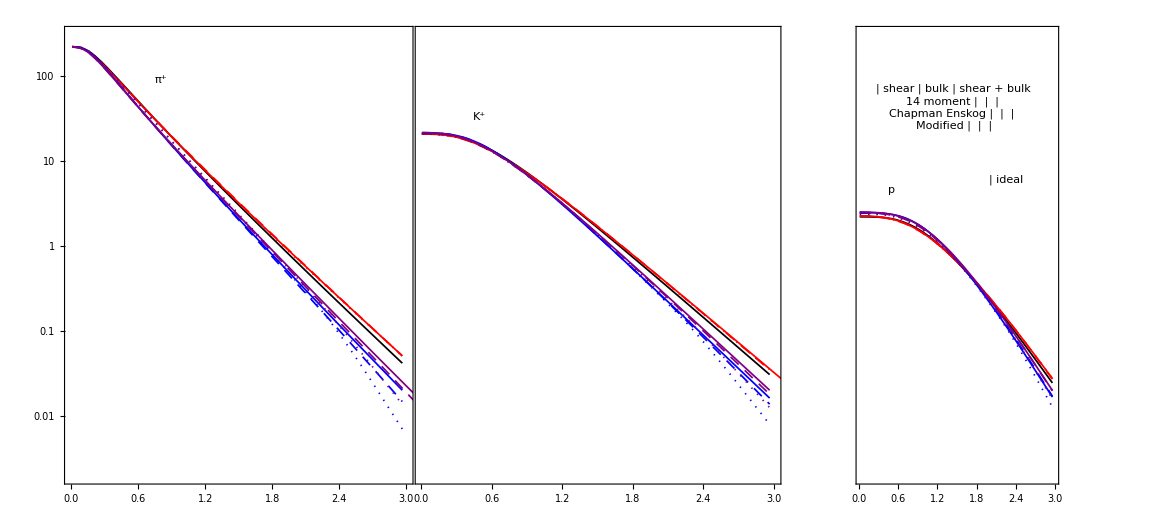
-Graphics-p_T (GeV)

```mathematica
SetDirectory@NotebookDirectory[];


pion = {idealπ,shear14π,shearCEπ,shearmodπ,bulk14π,bulkCEπ,bulkmodπ,shearbulk14π,shearbulkCEπ,shearbulkmodπ};
kaon= {idealK,shear14K,shearCEK,shearmodK,bulk14K,bulkCEK,bulkmodK,shearbulk14K,shearbulkCEK,shearbulkmodK};
proton={idealp,shear14p,shearCEp,shearmodp,bulk14p,bulkCEp,bulkmodp,shearbulk14p,shearbulkCEp,shearbulkmodp};

ratiopion = {ratioidealπ,ratioshear14π,ratioshearCEπ,ratioshearmodπ,ratiobulk14π,ratiobulkCEπ,ratiobulkmodπ,ratioshearbulk14π,ratioshearbulkCEπ,ratioshearbulkmodπ};
ratiokaon= {ratioidealK,ratioshear14K,ratioshearCEK,ratioshearmodK,ratiobulk14K,ratiobulkCEK,ratiobulkmodK,ratioshearbulk14K,ratioshearbulkCEK,ratioshearbulkmodK};
ratioproton={ratioidealp,ratioshear14p,ratioshearCEp,ratioshearmodp,ratiobulk14p,ratiobulkCEp,ratiobulkmodp, ratioshearbulk14p,ratioshearbulkCEp,ratioshearbulkmodp};



(*style={Directive[Black,AbsoluteThickness[1.5]],
Directive[Red,AbsoluteThickness[1.25],Dotted],Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{6,5}]],Directive[Red,AbsoluteThickness[1.25]],Directive[Blue,AbsoluteThickness[1.25],Dotted],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{6,5}]],Directive[Blue,AbsoluteThickness[1.25]]};*)

style={Directive[Black,AbsoluteThickness[1.25]],
Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Red,AbsoluteThickness[1.25]],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Blue,AbsoluteThickness[1.25]],
Directive[Purple,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Purple,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Purple,AbsoluteThickness[1.25]]};

styledf={Directive[Black,AbsoluteThickness[2]],
Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Red,AbsoluteThickness[2]],Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Blue,AbsoluteThickness[1.5]],
Directive[Purple,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Purple,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Purple,AbsoluteThickness[2]]};

(*legenddf=Panel[Grid[{{Graphics[{style[[1]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["ideal",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[2]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear mod",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[3]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear CE",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[4]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear 14",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[5]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk mod",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[6]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk CE",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[7]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk 14",FontSize->14,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];*)

legendπ=Panel[Grid[{{Style["π^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendK=Panel[Grid[{{Style["K^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendp=Panel[Grid[{{Style["p",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

dfsize=40;

legendideal = Panel[Grid[{{Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->14,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

legenddf=Panel[Grid[{{"",Style["shear",FontSize->14,FontFamily->"Arial"],Style["bulk",FontSize->14,FontFamily->"Arial"],Style["shear + bulk",FontSize->14,FontFamily->"Arial"]},

{Style["14 moment",FontSize->14,FontFamily->"Arial"],Graphics[{styledf[[2]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[5]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[8]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Chapman Enskog",FontSize->14,FontFamily->"Arial"],Graphics[{styledf[[3]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[6]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[9]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Modified",FontSize->14,FontFamily->"Arial"],Graphics[{styledf[[4]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[7]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[10]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]}(*,

{"","",Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->11,FontFamily->"Arial"]}*)}],Background->White,FrameMargins->0];

s ={0.0095,0};
l={0.016,0};

dNticks= {{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"0.01",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"0.1",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"1",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"10",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"100",l},{200,"",s}};

dNticksnone = {{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"",l},{200,"",s}};

a=30;
b=30;
ratiopionplot=ListPlot[ratiopion,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->200,AspectRatio->0.75,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];

ratiokaonplot=ListPlot[ratiokaon,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->200,AspectRatio->0.75,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];
ratioprotonplot=ListPlot[ratioproton,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->200,AspectRatio->0.75,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];

spectra=Panel[GraphicsGrid[{{

ListLogPlot[pion,PlotRange->{{0.0,3},{2.*10^-3,300}},Frame->True,FrameStyle->Black,FrameTicks->{{dNticks,dNticksnone},{Automatic,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendπ,{0.8,4.5}],Inset[ratiopionplot,{1.02,-3.3}]}, ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[kaon,PlotRange->{{0.01,3.0},{2.*10^-3,300}},Frame->True,FrameStyle->Black,FrameTicks->{{dNticksnone,dNticksnone},{True,All}},Joined->True,BaseStyle->{FontSize->14},InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendK,{0.5,3.5}],Inset[ratiokaonplot,{1.02,-3.3}]},ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[proton,PlotRange->{{0.01,3.0},{2.*10^-3,300}},Frame->True,FrameStyle->Black,FrameTicks->{{dNticksnone,dNticks},{True,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendp,{0.5,1.5}],Inset[ratioprotonplot,{1.02,-3.3}],Inset[legenddf,{1.45,3.75}],Inset[legendideal,{2.25,1.8}]},ImagePadding->{{a,b},{Automatic,Automatic}}]

}},Spacings->{-65.2,0},PlotLabel->Style["(dN/(2  π SubscriptBox[p, T] SubscriptBox[dp, T] dy))_(|_(y = 0))",FontSize->26,FontFamily->"Arial",Black]],{Style["p_T (GeV)",FontFamily->"Arial",FontSize->18]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]
Export["modified_spectra_500MeV.pdf",spectra];
```